# Reciprocal Multifactorial Constants

## Perfect matchings for K_ 6 and K_8

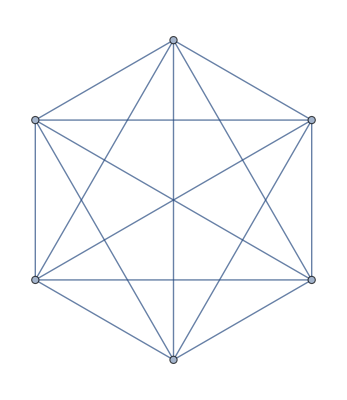

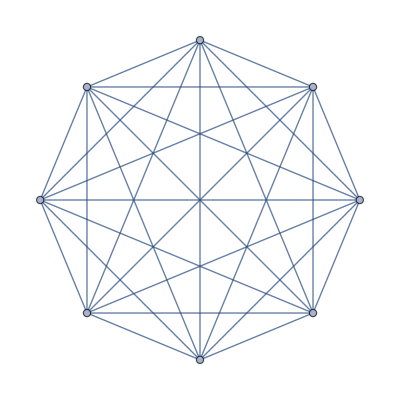

```mathematica
k6=CompleteGraph[6]
k8=CompleteGraph[8]
```

```mathematica
l6=Length[FindIndependentEdgeSet[k6]]
l8=Length[FindIndependentEdgeSet[k8]]
```

3

4

```mathematica
esl6=Select[Subsets[EdgeList[k6],{l6}],IndependentEdgeSetQ[k6,#]&]
esl8=Select[Subsets[EdgeList[k8],{l8}],IndependentEdgeSetQ[k8,#]&]
```

{{1<->2,3<->4,5<->6},{1<->2,3<->5,4<->6},{1<->2,3<->6,4<->5},{1<->3,2<->4,5<->6},{1<->3,2<->5,4<->6},{1<->3,2<->6,4<->5},{1<->4,2<->3,5<->6},{1<->4,2<->5,3<->6},{1<->4,2<->6,3<->5},{1<->5,2<->3,4<->6},{1<->5,2<->4,3<->6},{1<->5,2<->6,3<->4},{1<->6,2<->3,4<->5},{1<->6,2<->4,3<->5},{1<->6,2<->5,3<->4}}

{{1<->2,3<->4,5<->6,7<->8},{1<->2,3<->4,5<->7,6<->8},{1<->2,3<->4,5<->8,6<->7},{1<->2,3<->5,4<->6,7<->8},{1<->2,3<->5,4<->7,6<->8},{1<->2,3<->5,4<->8,6<->7},{1<->2,3<->6,4<->5,7<->8},{1<->2,3<->6,4<->7,5<->8},{1<->2,3<->6,4<->8,5<->7},{1<->2,3<->7,4<->5,6<->8},{1<->2,3<->7,4<->6,5<->8},{1<->2,3<->7,4<->8,5<->6},{1<->2,3<->8,4<->5,6<->7},{1<->2,3<->8,4<->6,5<->7},{1<->2,3<->8,4<->7,5<->6},{1<->3,2<->4,5<->6,7<->8},{1<->3,2<->4,5<->7,6<->8},{1<->3,2<->4,5<->8,6<->7},{1<->3,2<->5,4<->6,7<->8},{1<->3,2<->5,4<->7,6<->8},{1<->3,2<->5,4<->8,6<->7},{1<->3,2<->6,4<->5,7<->8},{1<->3,2<->6,4<->7,5<->8},{1<->3,2<->6,4<->8,5<->7},{1<->3,2<->7,4<->5,6<->8},{1<->3,2<->7,4<->6,5<->8},{1<->3,2<->7,4<->8,5<->6},{1<->3,2<->8,4<->5,6<->7},{1<->3,2<->8,4<->6,5<->7},{1<->3,2<->8,4<->7,5<->6},{1<->4,2<->3,5<->6,7<->8},{1<->4,2<->3,5<->7,6<->8},{1<->4,2<->3,5<->8,6<->7},{1<->4,2<->5,3<->6,7<->8},{1<->4,2<->5,3<->7,6<->8},{1<->4,2<->5,3<->8,6<->7},{1<->4,2<->6,3<->5,7<->8},{1<->4,2<->6,3<->7,5<->8},{1<->4,2<->6,3<->8,5<->7},{1<->4,2<->7,3<->5,6<->8},{1<->4,2<->7,3<->6,5<->8},{1<->4,2<->7,3<->8,5<->6},{1<->4,2<->8,3<->5,6<->7},{1<->4,2<->8,3<->6,5<->7},{1<->4,2<->8,3<->7,5<->6},{1<->5,2<->3,4<->6,7<->8},{1<->5,2<->3,4<->7,6<->8},{1<->5,2<->3,4<->8,6<->7},{1<->5,2<->4,3<->6,7<->8},{1<->5,2<->4,3<->7,6<->8},{1<->5,2<->4,3<->8,6<->7},{1<->5,2<->6,3<->4,7<->8},{1<->5,2<->6,3<->7,4<->8},{1<->5,2<->6,3<->8,4<->7},{1<->5,2<->7,3<->4,6<->8},{1<->5,2<->7,3<->6,4<->8},{1<->5,2<->7,3<->8,4<->6},{1<->5,2<->8,3<->4,6<->7},{1<->5,2<->8,3<->6,4<->7},{1<->5,2<->8,3<->7,4<->6},{1<->6,2<->3,4<->5,7<->8},{1<->6,2<->3,4<->7,5<->8},{1<->6,2<->3,4<->8,5<->7},{1<->6,2<->4,3<->5,7<->8},{1<->6,2<->4,3<->7,5<->8},{1<->6,2<->4,3<->8,5<->7},{1<->6,2<->5,3<->4,7<->8},{1<->6,2<->5,3<->7,4<->8},{1<->6,2<->5,3<->8,4<->7},{1<->6,2<->7,3<->4,5<->8},{1<->6,2<->7,3<->5,4<->8},{1<->6,2<->7,3<->8,4<->5},{1<->6,2<->8,3<->4,5<->7},{1<->6,2<->8,3<->5,4<->7},{1<->6,2<->8,3<->7,4<->5},{1<->7,2<->3,4<->5,6<->8},{1<->7,2<->3,4<->6,5<->8},{1<->7,2<->3,4<->8,5<->6},{1<->7,2<->4,3<->5,6<->8},{1<->7,2<->4,3<->6,5<->8},{1<->7,2<->4,3<->8,5<->6},{1<->7,2<->5,3<->4,6<->8},{1<->7,2<->5,3<->6,4<->8},{1<->7,2<->5,3<->8,4<->6},{1<->7,2<->6,3<->4,5<->8},{1<->7,2<->6,3<->5,4<->8},{1<->7,2<->6,3<->8,4<->5},{1<->7,2<->8,3<->4,5<->6},{1<->7,2<->8,3<->5,4<->6},{1<->7,2<->8,3<->6,4<->5},{1<->8,2<->3,4<->5,6<->7},{1<->8,2<->3,4<->6,5<->7},{1<->8,2<->3,4<->7,5<->6},{1<->8,2<->4,3<->5,6<->7},{1<->8,2<->4,3<->6,5<->7},{1<->8,2<->4,3<->7,5<->6},{1<->8,2<->5,3<->4,6<->7},{1<->8,2<->5,3<->6,4<->7},{1<->8,2<->5,3<->7,4<->6},{1<->8,2<->6,3<->4,5<->7},{1<->8,2<->6,3<->5,4<->7},{1<->8,2<->6,3<->7,4<->5},{1<->8,2<->7,3<->4,5<->6},{1<->8,2<->7,3<->5,4<->6},{1<->8,2<->7,3<->6,4<->5}}

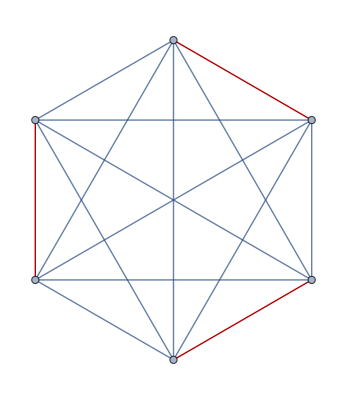
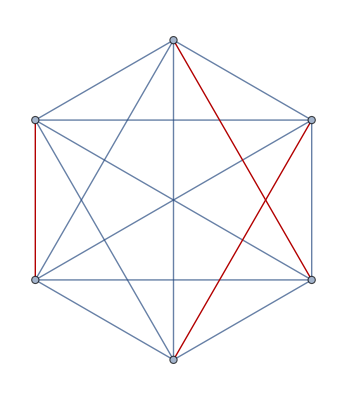
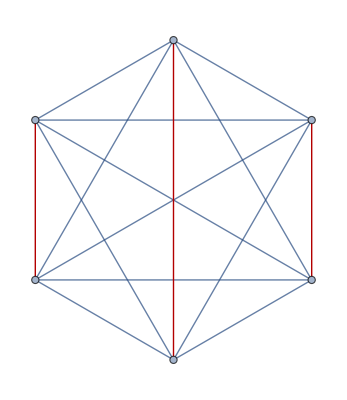
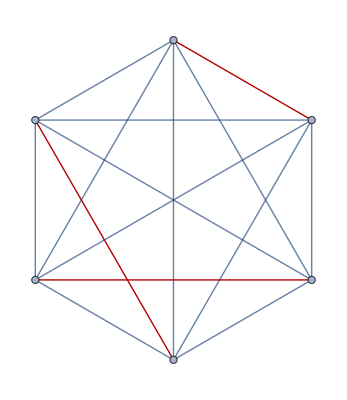
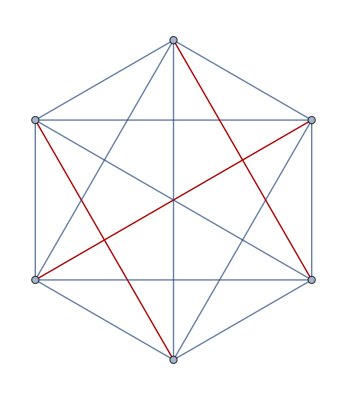
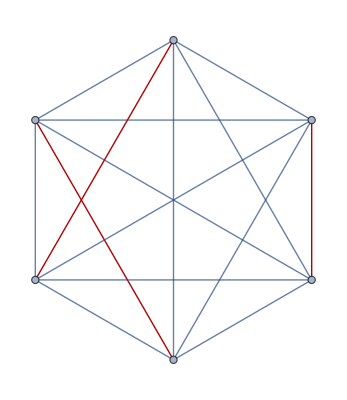
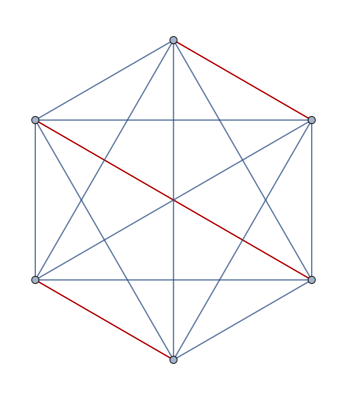
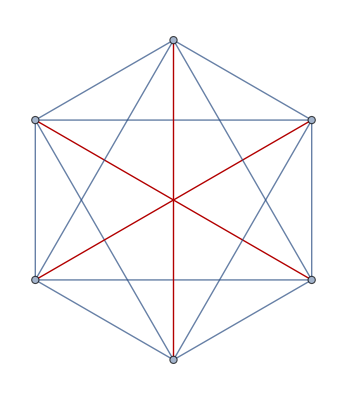
Grid[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]

```mathematica
Grid[Table[HighlightGraph[k6,h,GraphHighlightStyle->"Thick"],{h,esl6}]]
```

```mathematica
Grid[Table[HighlightGraph[k8,h,GraphHighlightStyle->"Thick"],{h,esl8}]]
```

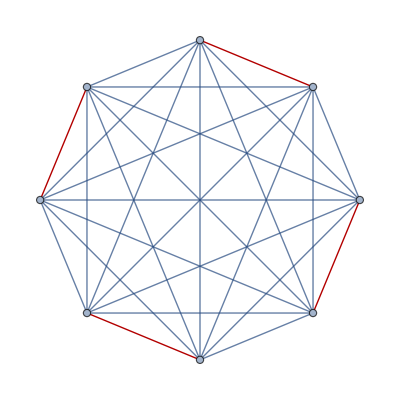
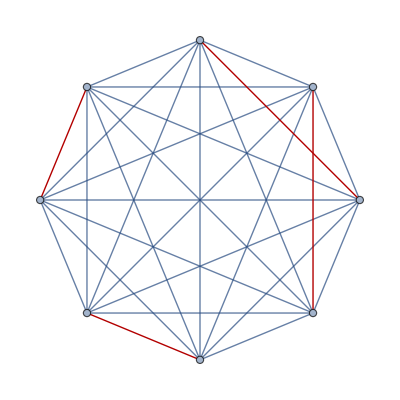
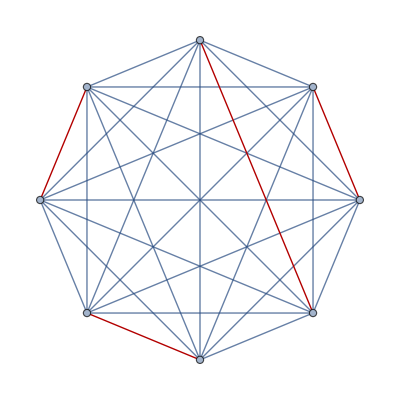
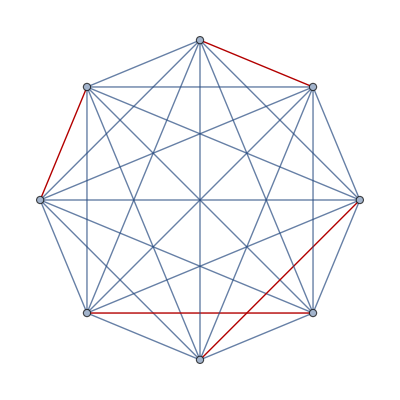
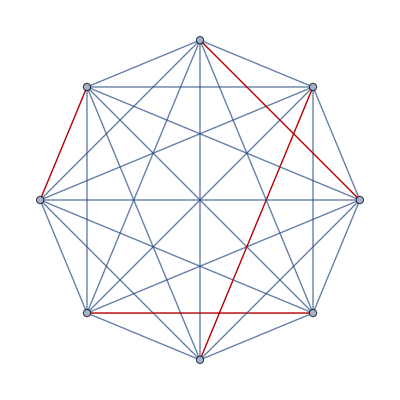
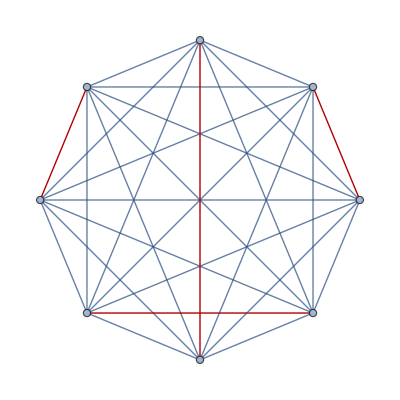
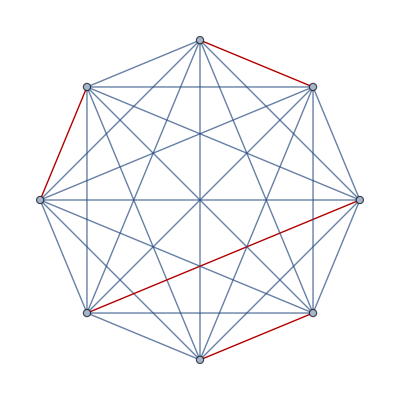
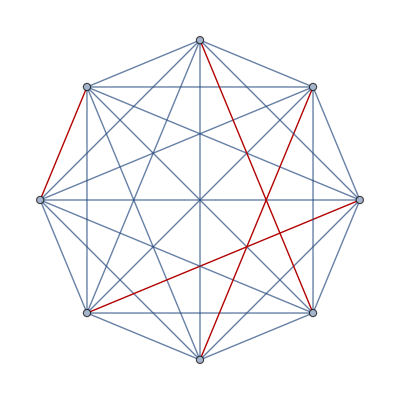

```mathematica
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-,,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

## Stirling Permutations

```mathematica
ClearAll[strlngPermutations]
strlngPermutations[1]={{1,1}};
strlngPermutations[k_]:=Join@@(Function[x,Flatten[Insert[x,{k,k},#]]&/@Range[2 k-1]]/@strlngPermutations[k-1])
```

```mathematica
Multicolumn[Sort@strlngPermutations@4,5,Appearance->"Horizontal"]
```

{1,1,2,2,3,3,4,4} | {1,1,2,2,3,4,4,3} | {1,1,2,2,4,4,3,3} | {1,1,2,3,3,2,4,4} | {1,1,2,3,3,4,4,2}
{1,1,2,3,4,4,3,2} | {1,1,2,4,4,2,3,3} | {1,1,2,4,4,3,3,2} | {1,1,3,3,2,2,4,4} | {1,1,3,3,2,4,4,2}
{1,1,3,3,4,4,2,2} | {1,1,3,4,4,3,2,2} | {1,1,4,4,2,2,3,3} | {1,1,4,4,2,3,3,2} | {1,1,4,4,3,3,2,2}
{1,2,2,1,3,3,4,4} | {1,2,2,1,3,4,4,3} | {1,2,2,1,4,4,3,3} | {1,2,2,3,3,1,4,4} | {1,2,2,3,3,4,4,1}
{1,2,2,3,4,4,3,1} | {1,2,2,4,4,1,3,3} | {1,2,2,4,4,3,3,1} | {1,2,3,3,2,1,4,4} | {1,2,3,3,2,4,4,1}
{1,2,3,3,4,4,2,1} | {1,2,3,4,4,3,2,1} | {1,2,4,4,2,1,3,3} | {1,2,4,4,2,3,3,1} | {1,2,4,4,3,3,2,1}
{1,3,3,1,2,2,4,4} | {1,3,3,1,2,4,4,2} | {1,3,3,1,4,4,2,2} | {1,3,3,2,2,1,4,4} | {1,3,3,2,2,4,4,1}
{1,3,3,2,4,4,2,1} | {1,3,3,4,4,1,2,2} | {1,3,3,4,4,2,2,1} | {1,3,4,4,3,1,2,2} | {1,3,4,4,3,2,2,1}
{1,4,4,1,2,2,3,3} | {1,4,4,1,2,3,3,2} | {1,4,4,1,3,3,2,2} | {1,4,4,2,2,1,3,3} | {1,4,4,2,2,3,3,1}
{1,4,4,2,3,3,2,1} | {1,4,4,3,3,1,2,2} | {1,4,4,3,3,2,2,1} | {2,2,1,1,3,3,4,4} | {2,2,1,1,3,4,4,3}
{2,2,1,1,4,4,3,3} | {2,2,1,3,3,1,4,4} | {2,2,1,3,3,4,4,1} | {2,2,1,3,4,4,3,1} | {2,2,1,4,4,1,3,3}
{2,2,1,4,4,3,3,1} | {2,2,3,3,1,1,4,4} | {2,2,3,3,1,4,4,1} | {2,2,3,3,4,4,1,1} | {2,2,3,4,4,3,1,1}
{2,2,4,4,1,1,3,3} | {2,2,4,4,1,3,3,1} | {2,2,4,4,3,3,1,1} | {2,3,3,2,1,1,4,4} | {2,3,3,2,1,4,4,1}
{2,3,3,2,4,4,1,1} | {2,3,3,4,4,2,1,1} | {2,3,4,4,3,2,1,1} | {2,4,4,2,1,1,3,3} | {2,4,4,2,1,3,3,1}
{2,4,4,2,3,3,1,1} | {2,4,4,3,3,2,1,1} | {3,3,1,1,2,2,4,4} | {3,3,1,1,2,4,4,2} | {3,3,1,1,4,4,2,2}
{3,3,1,2,2,1,4,4} | {3,3,1,2,2,4,4,1} | {3,3,1,2,4,4,2,1} | {3,3,1,4,4,1,2,2} | {3,3,1,4,4,2,2,1}
{3,3,2,2,1,1,4,4} | {3,3,2,2,1,4,4,1} | {3,3,2,2,4,4,1,1} | {3,3,2,4,4,2,1,1} | {3,3,4,4,1,1,2,2}
{3,3,4,4,1,2,2,1} | {3,3,4,4,2,2,1,1} | {3,4,4,3,1,1,2,2} | {3,4,4,3,1,2,2,1} | {3,4,4,3,2,2,1,1}
{4,4,1,1,2,2,3,3} | {4,4,1,1,2,3,3,2} | {4,4,1,1,3,3,2,2} | {4,4,1,2,2,1,3,3} | {4,4,1,2,2,3,3,1}
{4,4,1,2,3,3,2,1} | {4,4,1,3,3,1,2,2} | {4,4,1,3,3,2,2,1} | {4,4,2,2,1,1,3,3} | {4,4,2,2,1,3,3,1}
{4,4,2,2,3,3,1,1} | {4,4,2,3,3,2,1,1} | {4,4,3,3,1,1,2,2} | {4,4,3,3,1,2,2,1} | {4,4,3,3,2,2,1,1}

```mathematica
ClearAll[strlngPermGraph]
strlngPermGraph[sp_,opts:OptionsPattern[]]:=Module[{vl=DeleteDuplicates@sp,pos=PositionIndex@sp,eL=EdgeList@*TransitiveReductionGraph@*GraphUnion},Graph[Prepend[vl,0],eL[Graph@Thread[0->vl],SimpleGraph@RelationGraph[And@@Between[pos@#]/@pos[#2]&,vl]],GraphLayout->{"LayeredEmbedding","RootVertex"->0},EdgeLabels->{e_:>Placed[Last@e,{Left,"Middle"}]},opts]]
```

```mathematica
Grid[Partition[strlngPermGraph[#,PlotLabel->#, EdgeShapeFunction->"Line",EdgeStyle->Thick,EdgeLabelStyle->16,VertexSize->Medium]&/@strlngPermutations[3],5],Dividers->All, Spacings->{4, 4}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Partition[strlngPermGraph[#,PlotLabel->#, EdgeShapeFunction->"Line",EdgeStyle->Thick,EdgeLabelStyle->16,VertexSize->Medium]&/@strlngPermutations[4],8],Dividers->All, Spacings->{1,1}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Limits for Ratio test in m(2)

```mathematica
case1=(2^(1+2 n) n! (1+n)!)/(2 (1+n))!
case2=(2^(-1-2 n) (2 n)!)/(n! (1+n)!)
```

(2^(1+2 n) n! (1+n)!)/((2 (1+n))!)

(2^(-1-2 n) (2 n)!)/(n! (1+n)!)

```mathematica
limitm2case1=Limit[case1,n->Infinity]
limitm2case2=Limit[case2,n->Infinity]
```

0

0

## Computing m(1) to m(10) from n=0 to n=2000

```mathematica
Multifactorial[n_,k_]:=Abs[Apply[Times,Range[-n,-1,k]]]
```

```mathematica
For[i=1,i<11, i++, Print[N[Sum[1/Multifactorial[n,i],{n,0,150}], 20]]]
```

2.7182818284590452354

3.0594074053425761445

3.2989135380884190034

3.4859449774535577452

3.6402244677338097342

3.7719023962117584357

3.8869596537408434954

3.9892412126901365441

4.0813755201688985441

4.1652437655583845908

## Plot of m (1) to m (1) superimposed on each other from n = 0 to n = 2000

```mathematica
ListPlot[Table[Sum[1/Multifactorial[n,j],{n,1,i}],{j,1,10},{i,1,20}],PlotLegends->PointLegend[Automatic,PromptForm[k,#]&/@Range[10],LegendMarkers->{Graphics[Disk[]],6}]]
```

-Graphics-

```mathematica
ListPlot[Table[Sum[1/Multifactorial[n,j],{n,1,i}],{j,1,10},{i,1,50}],PlotLegends->PointLegend[Automatic,PromptForm[k,#]&/@Range[10],LegendMarkers->{Graphics[Disk[]],6}]]
```

-Graphics-

## Computation of RMFCs using the closed form formula

```mathematica
ClosedFormRMFC[n_]:=1+1/n Exp[1/n]Sum[n^(k/n)Gamma[k/n,0,1/n],{k,n}]
```

```mathematica
For[i=1,i<11, i++, Print[N[ClosedFormRMFC[i],20]]]
```

2.7182818284590452354

3.0594074053425761445

3.2989135380884190034

3.4859449774535577452

3.6402244677338097342

3.7719023962117584357

3.8869596537408434954

3.9892412126901365441

4.0813755201688985441

4.1652437655583845908

```mathematica
N[ClosedFormRMFC[100],100]
```

6.232555969004878175594833314474847191477721710732613036984586512592126592599921883112530488409940747

## Analysing efficiency of the two RMFC calculation methods

```mathematica
test1[xx_]:=(For[i=1,i<xx,i++,Print[N[Sum[1/Multifactorial[n,i],{n,0,250}],50]]//Inactive]//RepeatedTiming)[[1]]
test2[xx_]:=(For[i=1,i<xx,i++,Print[N[ClosedFormRMFC[i],50]]//Inactive]//RepeatedTiming)[[1]]
```

```mathematica
list1=ListPlot[Table[{xx,test1[xx]},{xx,1,100}],PlotRange->All,PlotLegends->{Automatic},AxesLabel->{"m(k)","time in sec"},PlotStyle->{Red,Thick}];
list2=ListPlot[Table[{xx,test2[xx]},{xx,1,100}],PlotRange->All,PlotLegends->{Automatic},AxesLabel->{"m(k)","time in sec"},PlotStyle->{Blue,Thick}];
```

```mathematica
Show[list1,list2, ImageSize->Large]
```

```mathematica
list3=ListPlot[Table[{xx,test1[xx]},{xx,1,200}],PlotRange->All,PlotLegends->{Automatic},AxesLabel->{"m(k)","time in sec"},PlotStyle->{Red,Thick}];
list4=ListPlot[Table[{xx,test2[xx]},{xx,1,200}],PlotRange->All,PlotLegends->{Automatic},AxesLabel->{"m(k)","time in sec"},PlotStyle->{Blue,Thick}];
```

```mathematica
Show[list3,list4, ImageSize->Large]
```

```mathematica
test3[xx_]:=(For[i=1,i<10,i++,Print[N[Sum[1/Multifactorial[n,i],{n,0,500}],xx]]//Inactive]//AbsoluteTiming)[[1]]
test4[xx_]:=(For[i=1,i<10,i++,Print[N[ClosedFormRMFC[i],xx]]//Inactive]//AbsoluteTiming)[[1]]
```

```mathematica
list5=ListPlot[Table[{xx,test3[xx]},{xx,1,100}],PlotRange->All,PlotLegends->{Automatic},AxesLabel->{"Digit Accuracy","time in sec"},PlotStyle->{Red,Thick}];
```

```mathematica
list6=ListPlot[Table[{xx,test4[xx]},{xx,1,100}],PlotRange->All,PlotLegends->{Automatic},AxesLabel->{"Digit Accuracy","time in sec"},PlotStyle->{Blue,Thick}];
```

```mathematica
Show[list5,list6, ImageSize->Large]
```

```mathematica
list7=ListPlot[Table[{xx,test3[xx]},{xx,1,200}],PlotRange->All,PlotLegends->{Automatic},AxesLabel->{"Digit Accuracy","time in sec"},PlotStyle->{Red,Thick}];
```

```mathematica
list8=ListPlot[Table[{xx,test4[xx]},{xx,1,200}],PlotRange->All,PlotLegends->{Automatic},AxesLabel->{"Digit Accuracy","time in sec"},PlotStyle->{Blue,Thick}];
```

```mathematica
Show[list7,list8, ImageSize->Large]
```

## Asymptotics of Reciprocal Multifactorial Series

### Simple Graph

```mathematica
ListPlot[Table[{x,ClosedFormRMFC[x]},{x,1,100}],ImageSize->Large,AxesLabel->{"k","m(k)"},PlotStyle->{Red,Thick}]
```

-Graphics-

### Detailed asymptotics

```mathematica
Series[1/k Integrate[((1-t) (1-E^(-( t/k))))/(t (E^(-(1/k Log[t]))-1)),{t,0,1}],{k,Infinity,5}]
```

Log[2]/k+(-1-Log[9/4])/(4 k^2)+(5+8 Log[4/3])/(48 k^3)+(-11-36 Log[5/4])/(864 k^4)+(-79+108 Log[6/5])/(12960 k^5)+O[1/k]^6

```mathematica
Series[HarmonicNumber[k],{k,Infinity,5}]
```

(EulerGamma+Log[k])+1/(2 k)-1/(12 k^2)+1/(120 k^4)+O[1/k]^6

```mathematica
FullSimplify[1+(1+1/(2 k^2)+1/k) (EulerGamma+1/(6 k^2)+1/(2 k)+Log[3]/(2 k^2)-Log[4]/(2 k)-Log[64]/(12 k^2)+Log[k])]
```

1+((1+2 k (1+k)) (1+Log[27/8]+k (3+6 EulerGamma k-Log[64])+6 k^2 Log[k]))/(12 k^4)

```mathematica
FullSimplify[1+(1+1/k)*((EulerGamma+Log[k]+1/(2k))-(1/k Log[2]))]
```

1+((1+k) (1+2 EulerGamma k-Log[4]+2 k Log[k]))/(2 k^2)

```mathematica
ClosedFormRMFC[n_]:=1+1/n Exp[1/n]Sum[n^(k/n)Gamma[k/n,0,1/n],{k,n}]
```

```mathematica
RMFCApproximation[k_]:=1+((1+2 k (1+k)) (1+Log[27/8]+k (3+6 EulerGamma k-Log[64])+6 k^2 Log[k]))/(12 k^4)
RMFCApproximation1[k_]:=1+((1+k) (1+2 EulerGamma k-2 Log[2]+2 k Log[k]))/(2 k^2)
```

```mathematica
N[RMFCApproximation[10]]
N[RMFCApproximation1[10]]
```

4.16492

4.14653

```mathematica
N[ClosedFormRMFC[10]]
```

4.16524

```mathematica
Table[{x,Abs[(N[ClosedFormRMFC[10^x]]-N[RMFCApproximation[10^x]])]/N[ClosedFormRMFC[10^x],50]},{x,0,5}]
```

{{0,0.0608426},{1,0.0000779859},{2,1.14278×10^-7},{3,1.29004×10^-10},{4,1.37156×10^-13},{5,0.}}

```mathematica
Table[{x,Abs[(N[ClosedFormRMFC[10^x]]-N[RMFCApproximation1[10^x]])]/N[ClosedFormRMFC[10^x],50]},{x,0,5}]
```

{{0,0.349539},{1,0.00449172},{2,0.0000476604},{3,4.84353×10^-7},{4,4.87866×10^-9},{5,4.90019×10^-11}}

## Generalized Reciprocal Multifactorial Constant

```mathematica
GRMFC[k_,x_]:=1+1/k Exp[x^k/k]Sum[k^(r/k)Gamma[r/k,0,x^k/k],{r,1,k}]
Multifactorial[n_,k_]:=Times@@Range[n,1,-k]
```

```mathematica
GRMFCsum[k_,x_,nn_]:=Sum[x^n/Multifactorial[n,k],{n,0,nn}]//N
```

```mathematica
Table[{ k,0.5 x,N[GRMFC[k,0.5x],5]},{k,1,5},{x,1,5}]
```

{{{1,0.5,1.64872},{1,1.,2.71828},{1,1.5,4.48169},{1,2.,7.38906},{1,2.5,12.1825}},{{2,0.5,1.67697},{2,1.,3.05941},{2,1.5,6.42488},{2,2.,16.2285},{2,2.5,50.9309}},{{3,0.5,1.68663},{3,1.,3.29891},{3,1.5,9.06146},{3,2.,45.7755},{3,2.5,589.3}},{{4,0.5,1.69039},{4,1.,3.48594},{4,1.5,13.1533},{4,2.,219.471},{4,2.5,70299.3}},{{5,0.5,1.69195},{5,1.,3.64022},{5,1.5,20.2725},{5,2.,2850.31},{5,2.5,1.43833×10^9}}}

```mathematica
Table[{ k,0.5 x,N[GRMFCsum[k,0.5x, 250],5]},{k,1,5},{x,1,5}]
```

{{{1,0.5,1.64872},{1,1.,2.71828},{1,1.5,4.48169},{1,2.,7.38906},{1,2.5,12.1825}},{{2,0.5,1.67697},{2,1.,3.05941},{2,1.5,6.42488},{2,2.,16.2285},{2,2.5,50.9309}},{{3,0.5,1.68663},{3,1.,3.29891},{3,1.5,9.06146},{3,2.,45.7755},{3,2.5,589.3}},{{4,0.5,1.69039},{4,1.,3.48594},{4,1.5,13.1533},{4,2.,219.471},{4,2.5,70299.3}},{{5,0.5,1.69195},{5,1.,3.64022},{5,1.5,20.2725},{5,2.,2850.31},{5,2.5,1.43833×10^9}}}